### Categorization

Tutorial

TBpack

TBpack`

TBpack/tutorial/MultiOrbitalCalculations

### Keywords

tight binding

tight-binding

few orbitals

multi-orbital

Hamiltonian

LCAO

linear combination of atomic orbitals

band structure

two center integrals

nearest neighbor approximation

crystals

periodic lattice

molecule

nanostructure

Details

# Multi-orbital Tight-binding Calculations

Fitting the experimental data with tight-binding calculations may require including the atomic orbitals laying below or above the frontier orbitals. In such cases, the set of basis functions must be extended by accounting for several orbitals per atom. This results in modification of the matrix Hamiltonian. This tutorial shows how such Hamiltonians can be constructed using TBpack core function Hamiltonian:

Hamiltonian[{unitcell_1,unitcell_2},opt_1→val_1,opt_2→val_2,...] | construct single-orbital tight-binding Hamiltonian using initial and optimized positions of atoms unitcell_1 and unitcell_2, subject to specified opt_i→val_i rules

Single-orbital matrix block construction.

### Band structure of a monolayer GaAs

As an example, we shall consider calculation of the electronic band structure of a monolayer GaAs, see M. Zhao, X. Chen, L. Li, and X. Zhang, Sci. Rep. 5, 8441 (2015); H.-C. Chung, C.-W. Chiu, and M.-F. Lin, Sci. Rep. 9, 2332 (2019).

2D GaAs lattice parameters:

```mathematica
a0=2.521; a=4.226;lz=0.633;a3=4.92;
a1=a {1/2,√3/2,0}; a2=a {1,0,0};
A={0,0,0}; B=(a1+a2)/3+lz {0,0,1};
{uc,T,a0} = {{A,B},{a1,a2},a0}
```

{{{0,0,0},{2.113,1.21994,0.633}},{{2.113,3.65982,0.},{4.226,0.,0.}},2.521}

This lattice has buckled structure:

```mathematica
Needs["TBpack`"]
```

```mathematica
n=3;
monoGaAs=Flatten[Table[i a1+j a2+#&/@uc,{i,-n,n},{j,-n,n}],2];
AtomicStructure[{monoGaAs,{},a0},BondLengthDelta->0.05]
```

-Graphics3D-

The correct description of GaAs requires accounting 3-orbitals per atom: |4s⟩, |4 p_x⟩, |4 p_y⟩. Thus, the Hamiltonian for the monolayer GaAs unit cell containing two atoms is a 6 by 6 matrix with a block structure:

(H_(s A, s A) | H_(s A, s B) | H_(s A, p_x A) | H_(s A, p_x B) | H_(s A, p_y A) | H_(s A, p_y B)
H_(s B, s A) | H_(s B, s B) | H_(s B, p_x A) | H_(s B, p_x B) | H_(s B, p_y A) | H_(s B, p_y B)
H_(p_x A, s A) | H_(p_x A, s B) | H_(p_x A, p_x A) | H_(p_x A, p_x B) | H_(p_x A, p_y A) | H_(p_x A, p_y B)
H_(p_x B, s A) | H_(p_x B, s B) | H_(p_x B, p_x A) | H_(p_x B, p_x B) | H_(p_x B, p_y A) | H_(p_x B, p_y B)
H_(p_y A, s A) | H_(p_y A, s B) | H_(p_y A, p_x A) | H_(p_y A, p_x B) | H_(p_y A, p_y A) | H_(p_y A, p_y B)
H_(p_y B, s A) | H_(p_y B, s B) | H_(p_y B, p_x A) | H_(p_y B, p_x B) | H_(p_y B, p_y A) | H_(p_y B, p_y B))

where A and B stand for Ga and As atoms, respectively.

Let us construct this Hamiltonian block by block.

Using Slater's notation for the hopping integrals, see J. C. Slater and G. F. Koster, Phys. Rev. 94, 1498 (1954), the tight-binding parameters are, see M. Zhao, X. Chen, L. Li, and X. Zhang, Sci. Rep. 5, 8441 (2015); H.-C. Chung, C.-W. Chiu, and M.-F. Lin, Sci. Rep. 9, 2332 (2019):

```mathematica
ϵ4sGa=-12.00;ϵ4pGa=-5.67;
ϵ4sAs=-17.68;ϵ4pAs=-8.30;
Vssσ=-1.707;
Vspσ=2.056;
Vppσ=2.65;
Vppπ=-0.827;
```

The first brown block (H_(s A, s A) | H_(s A, s B)
H_(s B, s A) | H_(s B, s B)) is

```mathematica
Clear[k];
hd={0,a0,a,a3};
test01=(#9===2&);
{Hss,Sss}=Hamiltonian[{uc,uc},
HoppingDistances->hd,
HoppingIntegrals-> {{ϵ4sGa,{ϵ4sAs,test01}},Vssσ,0,0},
OverlappingIntegrals->{{1,1},0,0,0},
TranslationVectors->{{a1,a2},{a1,a2}},Kpoint->k];
Chop[Hss]//MatrixForm
Chop[Sss]//MatrixForm
```

(-12. ⅇ^(ⅈ k.{0,0,0}) | -1.707 ⅇ^(ⅈ k.{-2.113,-1.21994,-0.633})-1.707 ⅇ^(ⅈ k.{0,2.43988,-0.633})-1.707 ⅇ^(ⅈ k.{2.113,-1.21994,-0.633})
-1.707 ⅇ^(ⅈ k.{-2.113,1.21994,0.633})-1.707 ⅇ^(ⅈ k.{0,-2.43988,0.633})-1.707 ⅇ^(ⅈ k.{2.113,1.21994,0.633}) | -17.68 ⅇ^(ⅈ k.{0,0,0}))

(ⅇ^(ⅈ k.{0,0,0}) | 0
0 | ⅇ^(ⅈ k.{0,0,0}))

Note: The above code uses hopping distances hd of the 2D GaAs monolayer and a test function test01 for the hopping integrals to distinguish Ga and As atoms. Here and in what follows the k-point is used in a symbolic form.

The remaining diagonal blocks (H_(p_i A, p_i A) | H_(p_i A, p_i B)
H_(p_i B, p_i A) | H_(p_i B, p_i B)), with i=x,y,  can be set up by specifying hopping integrals as pure functions defined as E_(x,x) from Table I in   J. C. Slater and G. F. Koster, Phys. Rev. 94, 1498 (1954):

```mathematica
Exx[x1_,y1_,z1_,x2_,y2_,z2_,nvec_,ppσ_,ppπ_]:=Block[{v={x2,y2,z2}-{x1,y1,z1},cosθ},cosθ=(v.nvec)/(√(v.v));
cosθ^2 ppσ+(1-cosθ^2) ppπ];
```

Now the two blue blocks can be constructed as follows:

```mathematica
Clear[k,Hpxpx,Spxpx,Hpypy,Spypy];
nvlist={{1,0,0},{0,1,0}};
Do[
nv=nvlist⟦Switch[i,"pxpx",1,"pypy",2]⟧;
hifun=Exx[#1,#2,#3,#4,#5,#6,nv,Vppσ,Vppπ]&;
{h,s}=Hamiltonian[{uc,uc},
HoppingDistances->hd,
HoppingIntegrals-> {{ϵ4pGa,{ϵ4pAs,test01}},hifun,0,0},
OverlappingIntegrals->{{1,1},0,0,0},
TranslationVectors->{{a1,a2},{a1,a2}},Kpoint->k];
Print[Chop[h]//MatrixForm];
Print[Chop[s]//MatrixForm];
Evaluate@{Symbol["H"<>i],Symbol["S"<>i]}={h,s},{i,{"pxpx","pypy"}}](* end Do *)
```

(-5.67 ⅇ^(ⅈ k.{0,0,0}) | 1.6163 ⅇ^(ⅈ k.{-2.113,-1.21994,-0.633})-0.827 ⅇ^(ⅈ k.{0,2.43988,-0.633})+1.6163 ⅇ^(ⅈ k.{2.113,-1.21994,-0.633})
1.6163 ⅇ^(ⅈ k.{-2.113,1.21994,0.633})-0.827 ⅇ^(ⅈ k.{0,-2.43988,0.633})+1.6163 ⅇ^(ⅈ k.{2.113,1.21994,0.633}) | -8.3 ⅇ^(ⅈ k.{0,0,0}))

(ⅇ^(ⅈ k.{0,0,0}) | 0
0 | ⅇ^(ⅈ k.{0,0,0}))

(-5.67 ⅇ^(ⅈ k.{0,0,0}) | -0.0125682 ⅇ^(ⅈ k.{-2.113,-1.21994,-0.633})+2.43073 ⅇ^(ⅈ k.{0,2.43988,-0.633})-0.0125682 ⅇ^(ⅈ k.{2.113,-1.21994,-0.633})
-0.0125682 ⅇ^(ⅈ k.{-2.113,1.21994,0.633})+2.43073 ⅇ^(ⅈ k.{0,-2.43988,0.633})-0.0125682 ⅇ^(ⅈ k.{2.113,1.21994,0.633}) | -8.3 ⅇ^(ⅈ k.{0,0,0}))

(ⅇ^(ⅈ k.{0,0,0}) | 0
0 | ⅇ^(ⅈ k.{0,0,0}))

The green off-diagonal blocks require setting hopping integrals as pure functions defined as E_(s,x) from Table I in J. C. Slater and G. F. Koster, Phys. Rev. 94, 1498 (1954):

```mathematica
Esx[x1_,y1_,z1_,x2_,y2_,z2_,nvec_,spσ_]:=Block[{v={x2,y2,z2}-{x1,y1,z1},cosθ},cosθ=(v.nvec)/(√(v.v));cosθ spσ];
```

These blocks are

```mathematica
Clear[k,Hspx,Hspy,Sspx,Sspy];
Do[
nv=nvlist⟦Switch[i,"spx",1,"spy",2]⟧;
hifun=Esx[#1,#2,#3,#4,#5,#6,nv,Vspσ]&;
{h,s}=Hamiltonian[{uc,uc},
HoppingDistances->hd,
HoppingIntegrals-> {0,hifun,0,0},
OverlappingIntegrals->{0,0,0,0},
TranslationVectors->{{a1,a2},{a1,a2}},Kpoint->k];
Print[Chop[h]//MatrixForm];
Print[Chop[s]//MatrixForm];
Evaluate@{Symbol["H"<>i],Symbol["S"<>i]}={h,s},{i,{"spx","spy"}}](* end Do *)
```

(0 | 1.72349 ⅇ^(ⅈ k.{-2.113,-1.21994,-0.633})-1.72349 ⅇ^(ⅈ k.{2.113,-1.21994,-0.633})
1.72349 ⅇ^(ⅈ k.{-2.113,1.21994,0.633})-1.72349 ⅇ^(ⅈ k.{2.113,1.21994,0.633}) | 0)

(0 | 0
0 | 0)

(0 | 0.995057 ⅇ^(ⅈ k.{-2.113,-1.21994,-0.633})-1.99011 ⅇ^(ⅈ k.{0,2.43988,-0.633})+0.995057 ⅇ^(ⅈ k.{2.113,-1.21994,-0.633})
-0.995057 ⅇ^(ⅈ k.{-2.113,1.21994,0.633})+1.99011 ⅇ^(ⅈ k.{0,-2.43988,0.633})-0.995057 ⅇ^(ⅈ k.{2.113,1.21994,0.633}) | 0)

(0 | 0
0 | 0)

Finally, we can construct the off-diagonal block for p_x and p_y orbitals.

The hopping integrals are given by E_(x,y) from Table I in J. C. Slater and G. F. Koster, Phys. Rev. 94, 1498 (1954):

```mathematica
Exy[x1_,y1_,z1_,x2_,y2_,z2_,nvec1_,nvec2_,ppσ_,ppπ_]:=Block[{v={x2,y2,z2}-{x1,y1,z1},cosθ1,cosθ2},
cosθ1=(v.nvec1)/(√(v.v));
cosθ2=(v.nvec2)/(√(v.v));
(ppσ-ppπ) cosθ1 cosθ2];
```

Hence

```mathematica
Clear[k,Hpxpy,Spxpy];

nv1={1,0,0};
nv2={0,1,0};
hifun=Exy[#1,#2,#3,#4,#5,#6,nv1,nv2,Vppσ,Vppπ]&;
{h,s}=Hamiltonian[{uc,uc},
HoppingDistances->hd,
HoppingIntegrals-> {0,hifun,0,0},
OverlappingIntegrals->{0,0,0,0},
TranslationVectors->{{a1,a2},{a1,a2}},Kpoint->k];
Print[Chop[h]//MatrixForm];
Print[Chop[s]//MatrixForm];
{Hpxpy,Spxpy}={h,s};
```

(0 | 1.41064 ⅇ^(ⅈ k.{-2.113,-1.21994,-0.633})-1.41064 ⅇ^(ⅈ k.{2.113,-1.21994,-0.633})
-1.41064 ⅇ^(ⅈ k.{-2.113,1.21994,0.633})+1.41064 ⅇ^(ⅈ k.{2.113,1.21994,0.633}) | 0)

(0 | 0
0 | 0)

Thus, the full Hamiltonian is

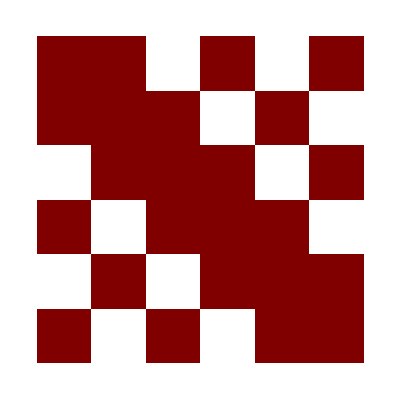

```mathematica
H=Flatten[{
{Hss,Hspx,Hspy},
{ConjugateTranspose[Hspx],Hpxpx,Hpxpy},
{ConjugateTranspose[Hspy],ConjugateTranspose[Hpxpy],Hpypy}
},{{1,3},{2,4}}];

ArrayPlot[H]
```

Next we need to solve the eigenvalue problem for the constructed Hamiltonian for a range of k-points.

To do this, we sample the path through the high symmetry M-Γ-K-M of the Brillouin zone of monolayer GaAs (2D honeycomb lattice):

```mathematica
Γ={0,0,0};
K={4π/(3a),0,0};
M={π/a,-π/(√3 a),0};
np=40;
klist=Join[Table[(Γ-M)i/np+M,{i,np}],Table[(K-Γ)i/np+Γ,{i,np}],Table[(M-K)i/np+K,{i,np}]];
```

and solve the problem with Eigenvalues :

```mathematica
bands=Transpose[Table[Sort@Chop@Eigenvalues[H/.k->klist⟦i⟧],{i,Length[klist]}]];
```

For the purpose of visualization, we define the Fermi level as the top of the valence band and find the band gap:

```mathematica
Ef=bands⟦3⟧//Max
cbmin=bands⟦4⟧//Min
Eg=cbmin-Ef
```

-9.72655

-8.98421

0.742336

Now the electronic band structure can be plotted with a highlighted band gap. Using ListPlot we have

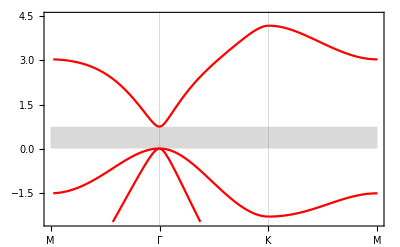

```mathematica
ListLinePlot[bands-Ef,
PlotStyle->Red,Axes->False,Frame->True,
PlotRange->{-2.5,4.5},
FrameTicks->{{{0,"M"},{40,"Γ"},{80,"K"},{120,"M"}},Automatic},GridLines->{{40,80},None},Prolog->{EdgeForm[None],FaceForm[LightGray],Rectangle[{0,0},{120,Eg}]}]
```

The obtained band structure is the same as the band structure neglecting spin-orbit coupling in Fig. 1(c) of  H.-C. Chung, C.-W. Chiu, and M.-F. Lin, Sci. Rep. 9, 2332 (2019) and Fig. 2 (a)  M. Zhao, X. Chen, L. Li, and X. Zhang, Sci. Rep. 5, 8441 (2015).

It is also instructive to compare this bands structure with that of a bulk GaAs. The band structures of the monolayer and bulk GaAs are qualitatively the same. The major difference is the size of the band gap that is 0.74 eV for the former and 1.42 eV for the latter.

### Graphene band structure including σ-bands

As a second example, we consider the band structure of graphene that contains not only π-bands but also σ-bands, see Sec. 2.3.2 in R. Saito, G. Dresselhaus, and M. Dresselhaus, Physical Properties of Carbon Nanotubes (Imperial College Press, London, 1998) and Sec. II in R. Saito, M. Fujita, G. Dresselhaus, and M. S. Dresselhaus, Phys. Rev. B 46, 1804 (1992).

This is, by and large, a repetition of the algorithm used in the previous section "Band structure of a monolayer GaAs". The major difference is the usage of an extended atomic orbital basis and a larger number of the phenomenological parameters that includes not only two-center hopping but also overlapping integrals. Taking this into account, we gather the required two-center integrals E_(s,x), E_(x,x), E_(x,y) from Table I in J. C. Slater and G. F. Koster, Phys. Rev. 94, 1498 (1954) in a preliminary section 'Two-center integrals'.

Two-center integrals

```mathematica
Esx[x1_,y1_,z1_,x2_,y2_,z2_,nvec_,spσ_]:=Block[{v={x2,y2,z2}-{x1,y1,z1},cosθ},cosθ=(v.nvec)/(√(v.v));cosθ spσ];

Exx[x1_,y1_,z1_,x2_,y2_,z2_,nvec_,ppσ_,ppπ_]:=Block[{v={x2,y2,z2}-{x1,y1,z1},cosθ},cosθ=(v.nvec)/(√(v.v));
cosθ^2 ppσ+(1-cosθ^2) ppπ];

Exy[x1_,y1_,z1_,x2_,y2_,z2_,nvec1_,nvec2_,ppσ_,ppπ_]:=Block[{v={x2,y2,z2}-{x1,y1,z1},cosθ1,cosθ2},
cosθ1=(v.nvec1)/(√(v.v));
cosθ2=(v.nvec2)/(√(v.v));
(ppσ-ppπ) cosθ1 cosθ2];
```

Graphene honeycomb lattice parameters are

```mathematica
a0=1.42; a=√3 a0;
a1=a {1/2,√3/2,0}; a2=a {1,0,0};
A={0,0,0}; B=(a1+a2)/3;
{guc,T,a0} = {{A,B},{a1,a2},a0}
```

{{{0,0,0},{1.22976,0.71,0.}},{{1.22976,2.13,0.},{2.45951,0.,0.}},1.42}

We choose a wave function basis as a set of four orbitals:  |2s⟩, |2 p_x⟩, |2 p_y⟩, |2 p_z⟩. Hence, the matrix Hamiltonian for the two atom unit cell of graphene is an 8 by 8 matrix with the following block structure:

(H_(s A, s A) | H_(s A, s B) | H_(s A, p_x A) | H_(s A, p_x B) | H_(s A, p_y A) | H_(s A, p_y B) | H_(s A, p_z A) | H_(s A, p_z B)
H_(s B, s A) | H_(s B, s B) | H_(s B, p_x A) | H_(s B, p_x B) | H_(s B, p_y A) | H_(s B, p_y B) | H_(s B, p_z A) | H_(s B, p_z B)
H_(p_x A, s A) | H_(p_x A, s B) | H_(p_x A, p_x A) | H_(p_x A, p_x B) | H_(p_x A, p_y A) | H_(p_x A, p_y B) | H_(p_x A, p_z A) | H_(p_x A, p_z B)
H_(p_x B, s A) | H_(p_x B, s B) | H_(p_x B, p_x A) | H_(p_x B, p_x B) | H_(p_x B, p_y A) | H_(p_x B, p_y B) | H_(p_x B, p_z A) | H_(p_x B, p_z B)
H_(p_y A, s A) | H_(p_y A, s B) | H_(p_y A, p_x A) | H_(p_y A, p_x B) | H_(p_y A, p_y A) | H_(p_y A, p_y B) | H_(p_y A, p_z A) | H_(p_y A, p_z B)
H_(p_y B, s A) | H_(p_y B, s B) | H_(p_y B, p_x A) | H_(p_y B, p_x B) | H_(p_y B, p_y A) | H_(p_y B, p_y B) | H_(p_y B, p_z A) | H_(p_y B, p_z B)
H_(p_z A, s A) | H_(p_z A, s B) | H_(p_z A, p_x A) | H_(p_z A, p_x B) | H_(p_z A, p_y A) | H_(p_z A, p_y B) | H_(p_z A, p_z A) | H_(p_z A, p_z B)
H_(p_z B, s A) | H_(p_z B, s B) | H_(p_z B, p_x A) | H_(p_z B, p_x B) | H_(p_z B, p_y A) | H_(p_z B, p_y B) | H_(p_z B, p_z A) | H_(p_z B, p_z B))

where A and B denote the two non-equivalent sites of the graphene honeycomb lattice.

Let us construct this Hamiltonian block by block.

To do this, we need the tight-binding parameters from Table 2.1 on page 32 in  R. Saito, G. Dresselhaus, and M. Dresselhaus, Physical Properties of Carbon Nanotubes (Imperial College Press, London, 1998):

```mathematica
ϵ2s=-8.868;ϵ2p=0;
ℋss=-6.769;𝒮ss=0.212;
ℋsp=-5.58;𝒮sp=0.102;
ℋσ=5.037;𝒮σ=-0.146;
ℋπ=-3.033;𝒮π=0.129;
```

Warning: Here ℋσ and 𝒮σ have opposite signs as compared to those in both Table 2.1 in R. Saito, G. Dresselhaus, and M. Dresselhaus, Physical Properties of Carbon Nanotubes (Imperial College Press, London, 1998) and Table II in  R. Saito, M. Fujita, G. Dresselhaus, and M. S. Dresselhaus, Phys. Rev. B 46, 1804 (1992). This sign correction is the only way to reproduce the reported band structures in the mentioned works, therefore we consider this correction as a correction of the misprint in the original published materials.

Note: The above parameters ℋss, ℋsp, ℋσ, and ℋπ correspond to ssσ, spσ, ppσ and ppπ in the Slater's notation, see Sec. III in J. C. Slater and G. F. Koster, Phys. Rev. 94, 1498 (1954)

The top-left brown block (H_(s A, s A) | H_(s A, s B)
H_(s B, s A) | H_(s B, s B)) is

```mathematica
Needs["TBpack`"]
```

```mathematica
Clear[k,Hss,Sss];
{Hss,Sss}=Hamiltonian[{guc,guc},
HoppingIntegrals-> {ϵ2s,ℋss,0,0},
OverlappingIntegrals->{1,𝒮ss,0,0},
TranslationVectors->{{a1,a2},{a1,a2}},Kpoint->k];
Print["Hss=",Chop[Hss]//MatrixForm]
Print["Sss=",Chop[Sss]//MatrixForm]
```

Hss=(-8.868 ⅇ^(ⅈ k.{0,0,0}) | -6.769 ⅇ^(ⅈ k.{-1.22976,-0.71,0})-6.769 ⅇ^(ⅈ k.{0,1.42,0})-6.769 ⅇ^(ⅈ k.{1.22976,-0.71,0})
-6.769 ⅇ^(ⅈ k.{-1.22976,0.71,0})-6.769 ⅇ^(ⅈ k.{0,-1.42,0})-6.769 ⅇ^(ⅈ k.{1.22976,0.71,0}) | -8.868 ⅇ^(ⅈ k.{0,0,0}))

Sss=(ⅇ^(ⅈ k.{0,0,0}) | 0.212 ⅇ^(ⅈ k.{-1.22976,-0.71,0})+0.212 ⅇ^(ⅈ k.{0,1.42,0})+0.212 ⅇ^(ⅈ k.{1.22976,-0.71,0})
0.212 ⅇ^(ⅈ k.{-1.22976,0.71,0})+0.212 ⅇ^(ⅈ k.{0,-1.42,0})+0.212 ⅇ^(ⅈ k.{1.22976,0.71,0}) | ⅇ^(ⅈ k.{0,0,0}))

The blue diagonal blocks are

```mathematica
Clear[k,Hpxpx,Spxpx,Hpypy,Spypy,Hpzpz,Spzpz];
nvlist={{1,0,0},{0,1,0},{0,0,1}};
Do[
nv=nvlist⟦Switch[i,"pxpx",1,"pypy",2,"pzpz",3]⟧;
hifun=Exx[#1,#2,#3,#4,#5,#6,nv,ℋσ,ℋπ]&;
oifun=Exx[#1,#2,#3,#4,#5,#6,nv,𝒮σ,𝒮π]&;
{h,s}=Hamiltonian[{guc,guc},
HoppingIntegrals-> {ϵ2p,hifun,0,0},
OverlappingIntegrals->{1,oifun,0,0},
TranslationVectors->{{a1,a2},{a1,a2}},Kpoint->k];
Print["H"<>i<>"=",Chop[h]//MatrixForm];
Print["S"<>i<>"=",Chop[s]//MatrixForm];
Evaluate@{Symbol["H"<>i],Symbol["S"<>i]}={h,s},{i,{"pxpx","pypy","pzpz"}}](* end Do *)
```

Hpxpx=(0 | 3.0195 ⅇ^(ⅈ k.{-1.22976,-0.71,0})-3.033 ⅇ^(ⅈ k.{0,1.42,0})+3.0195 ⅇ^(ⅈ k.{1.22976,-0.71,0})
3.0195 ⅇ^(ⅈ k.{-1.22976,0.71,0})-3.033 ⅇ^(ⅈ k.{0,-1.42,0})+3.0195 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Spxpx=(ⅇ^(ⅈ k.{0,0,0}) | -0.07725 ⅇ^(ⅈ k.{-1.22976,-0.71,0})+0.129 ⅇ^(ⅈ k.{0,1.42,0})-0.07725 ⅇ^(ⅈ k.{1.22976,-0.71,0})
-0.07725 ⅇ^(ⅈ k.{-1.22976,0.71,0})+0.129 ⅇ^(ⅈ k.{0,-1.42,0})-0.07725 ⅇ^(ⅈ k.{1.22976,0.71,0}) | ⅇ^(ⅈ k.{0,0,0}))

Hpypy=(0 | -1.0155 ⅇ^(ⅈ k.{-1.22976,-0.71,0})+5.037 ⅇ^(ⅈ k.{0,1.42,0})-1.0155 ⅇ^(ⅈ k.{1.22976,-0.71,0})
-1.0155 ⅇ^(ⅈ k.{-1.22976,0.71,0})+5.037 ⅇ^(ⅈ k.{0,-1.42,0})-1.0155 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Spypy=(ⅇ^(ⅈ k.{0,0,0}) | 0.06025 ⅇ^(ⅈ k.{-1.22976,-0.71,0})-0.146 ⅇ^(ⅈ k.{0,1.42,0})+0.06025 ⅇ^(ⅈ k.{1.22976,-0.71,0})
0.06025 ⅇ^(ⅈ k.{-1.22976,0.71,0})-0.146 ⅇ^(ⅈ k.{0,-1.42,0})+0.06025 ⅇ^(ⅈ k.{1.22976,0.71,0}) | ⅇ^(ⅈ k.{0,0,0}))

Hpzpz=(0 | -3.033 ⅇ^(ⅈ k.{-1.22976,-0.71,0})-3.033 ⅇ^(ⅈ k.{0,1.42,0})-3.033 ⅇ^(ⅈ k.{1.22976,-0.71,0})
-3.033 ⅇ^(ⅈ k.{-1.22976,0.71,0})-3.033 ⅇ^(ⅈ k.{0,-1.42,0})-3.033 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Spzpz=(ⅇ^(ⅈ k.{0,0,0}) | 0.129 ⅇ^(ⅈ k.{-1.22976,-0.71,0})+0.129 ⅇ^(ⅈ k.{0,1.42,0})+0.129 ⅇ^(ⅈ k.{1.22976,-0.71,0})
0.129 ⅇ^(ⅈ k.{-1.22976,0.71,0})+0.129 ⅇ^(ⅈ k.{0,-1.42,0})+0.129 ⅇ^(ⅈ k.{1.22976,0.71,0}) | ⅇ^(ⅈ k.{0,0,0}))

The green off-diagonal blocks are

```mathematica
Clear[k,Hspx,Sspx,Hspy,Sspy,Hspz,Sspz];
Do[
nv=nvlist⟦Switch[i,"spx",1,"spy",2,"spz",3]⟧;
hifun=Esx[#1,#2,#3,#4,#5,#6,nv,ℋsp]&;oifun=Esx[#1,#2,#3,#4,#5,#6,nv,𝒮sp]&;
{h,s}=Hamiltonian[{guc,guc},
HoppingIntegrals-> {0,hifun,0,0},
OverlappingIntegrals->{0,oifun,0,0},
TranslationVectors->{{a1,a2},{a1,a2}},Kpoint->k];
Print["H"<>i<>"=",Chop[h]//MatrixForm];
Print["S"<>i<>"=",Chop[s]//MatrixForm];
Evaluate@{Symbol["H"<>i],Symbol["S"<>i]}={h,s},{i,{"spx","spy","spz"}}](* end Do *)
```

Hspx=(0 | -4.83242 ⅇ^(ⅈ k.{-1.22976,-0.71,0})+4.83242 ⅇ^(ⅈ k.{1.22976,-0.71,0})
-4.83242 ⅇ^(ⅈ k.{-1.22976,0.71,0})+4.83242 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Sspx=(0 | 0.0883346 ⅇ^(ⅈ k.{-1.22976,-0.71,0})-0.0883346 ⅇ^(ⅈ k.{1.22976,-0.71,0})
0.0883346 ⅇ^(ⅈ k.{-1.22976,0.71,0})-0.0883346 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Hspy=(0 | -2.79 ⅇ^(ⅈ k.{-1.22976,-0.71,0})+5.58 ⅇ^(ⅈ k.{0,1.42,0})-2.79 ⅇ^(ⅈ k.{1.22976,-0.71,0})
2.79 ⅇ^(ⅈ k.{-1.22976,0.71,0})-5.58 ⅇ^(ⅈ k.{0,-1.42,0})+2.79 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Sspy=(0 | 0.051 ⅇ^(ⅈ k.{-1.22976,-0.71,0})-0.102 ⅇ^(ⅈ k.{0,1.42,0})+0.051 ⅇ^(ⅈ k.{1.22976,-0.71,0})
-0.051 ⅇ^(ⅈ k.{-1.22976,0.71,0})+0.102 ⅇ^(ⅈ k.{0,-1.42,0})-0.051 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Hspz=(0 | 0
0 | 0)

Sspz=(0 | 0
0 | 0)

The magenta off-diagonal blocks are

```mathematica
Clear[k,Hpxpy,Spxpy,Hpxpz,Spxpz,Hpypz,Spypz]
nvlist1={{1,0,0},{1,0,0},{0,1,0}};
nvlist2={{0,1,0},{0,0,1},{0,0,1}};
lbls={"23","24","34"};
Do[
ind=Switch[i,"pxpy",1,"pxpz",2,"pypz",3];
nv1=nvlist1⟦ind⟧;
nv2=nvlist2⟦ind⟧;
hifun=Exy[#1,#2,#3,#4,#5,#6,nv1,nv2,ℋσ,ℋπ]&;
oifun=Exy[#1,#2,#3,#4,#5,#6,nv1,nv2,𝒮σ,𝒮π]&;
{h,s}=Hamiltonian[{guc,guc},
HoppingIntegrals-> {0,hifun,0,0},
OverlappingIntegrals->{0,oifun,0,0},
TranslationVectors->{{a1,a2},{a1,a2}},Kpoint->k];
Print["H"<>i<>"=",Chop[h]//MatrixForm];
Print["S"<>i<>"=",Chop[s]//MatrixForm];
Evaluate@{Symbol["H"<>i],Symbol["S"<>i]}={h,s},{i,{"pxpy","pxpz","pypz"}}](* end Do *)
```

Hpxpy=(0 | 3.49441 ⅇ^(ⅈ k.{-1.22976,-0.71,0})-3.49441 ⅇ^(ⅈ k.{1.22976,-0.71,0})
-3.49441 ⅇ^(ⅈ k.{-1.22976,0.71,0})+3.49441 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Spxpy=(0 | -0.119078 ⅇ^(ⅈ k.{-1.22976,-0.71,0})+0.119078 ⅇ^(ⅈ k.{1.22976,-0.71,0})
0.119078 ⅇ^(ⅈ k.{-1.22976,0.71,0})-0.119078 ⅇ^(ⅈ k.{1.22976,0.71,0}) | 0)

Hpxpz=(0 | 0
0 | 0)

Spxpz=(0 | 0
0 | 0)

Hpypz=(0 | 0
0 | 0)

Spypz=(0 | 0
0 | 0)

By assembling all the building blocks of the Hamiltonian and matrix of atomic orbitals overlaps, we obtain

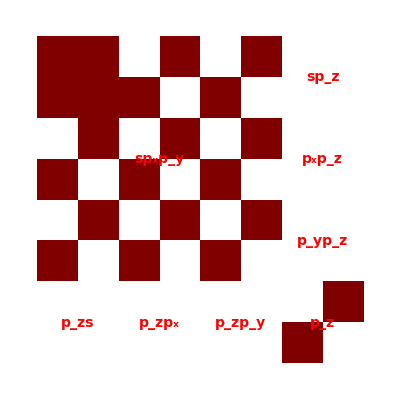
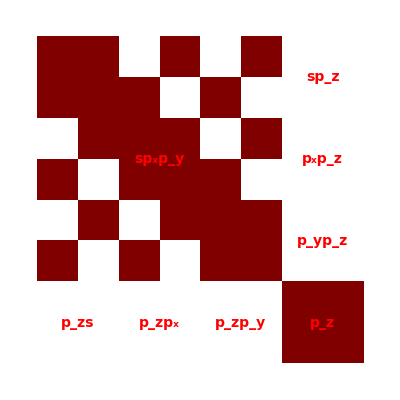

```mathematica
H=Flatten[{
{Hss,Hspx,Hspy,Hspz},
{ConjugateTranspose[Hspx],Hpxpx,Hpxpy,Hpxpz},{ConjugateTranspose[Hspy],ConjugateTranspose[Hpxpy],Hpypy,Hpypz},{ConjugateTranspose[Hspz],ConjugateTranspose[Hpxpz],ConjugateTranspose[Hpypz],Hpzpz}
},{{1,3},{2,4}}];
S=Flatten[{
{Sss,Sspx,Sspy,Sspz},{ConjugateTranspose[Sspx],Spxpx,Spxpy,Spxpz},{ConjugateTranspose[Sspy],ConjugateTranspose[Spxpy],Spypy,Spypz},{ConjugateTranspose[Sspz],ConjugateTranspose[Spxpz],ConjugateTranspose[Spypz],Spzpz}
},{{1,3},{2,4}}];

sz=14;cl=Red;dir={1,1};
lblfun=Text[Style[#1,sz,Bold,cl],#2,{0,0},dir]&;

ArrayPlot[#,Epilog->{lblfun["sp_xp_y",{3,5}],lblfun["sp_z",{7,7}],lblfun["p_xp_z",{7,5}],
lblfun["p_yp_z",{7,3}],lblfun["p_zs",{1,1}],lblfun["p_zp_x",{3,1}],lblfun["p_zp_y",{5,1}],lblfun["p_z",{7,1}]
}]&/@{H,S}
```

As one can see the σ-bands are fully decoupled from π-bands, since the 2 by 2 p_z-orbital block (the bottom-right) is isolated form the 6 by 6 sp_x p_y-block by zero 2 by 2 sp_z-(p_z s-), p_x p_z-(p_z p_x-) and p_y p_z-(p_z p_y-)blocks for both the Hamiltonian and matrix of atomic orbitals overlaps.

Now we can solve the generalized eigenvalue problem for the constructed Hamiltonian and the matrix of atomic orbitals overlaps for a range of k-points.

The first Brillouin zone is sampled with k-points only along the lines connecting the high symmetry points K-Γ-M-K:

```mathematica
Γ={0,0,0};
K={4π/(3a),0,0};
M={π/a,-π/(√3 a),0};
np=20;
klist=Join[Table[(Γ-K)i/np+K,{i,np}],Table[(M-Γ)i/np+Γ,{i,np}],Table[(K-M)i/np+M,{i,np}]];
```

The energy bands along the sampled lines can be found with Eigenvalues and sorted with Sort:

```mathematica
bands=Table[Sort@Chop@Eigenvalues[{H,S}/.k->klist⟦i⟧],{i,Length[klist]}];
```

Finally, we can visualise the bands with ListLinePlot:

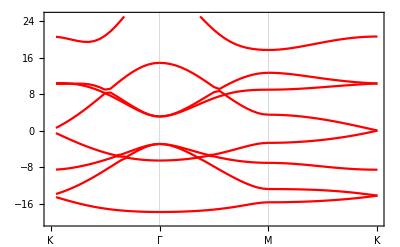

```mathematica
ListLinePlot[Transpose[bands],
PlotStyle->Red,Axes->False,Frame->True,PlotRange->{-20,25},FrameTicks->{{{0,"K"},{20,"Γ"},{40,"M"},{60,"K"}},Automatic},GridLines->{{20,40},None}]
```

The fact that the σ- and π-bands in graphene are fully decoupled allows one also to find them separately and then combine in one plot without losing any information about them:

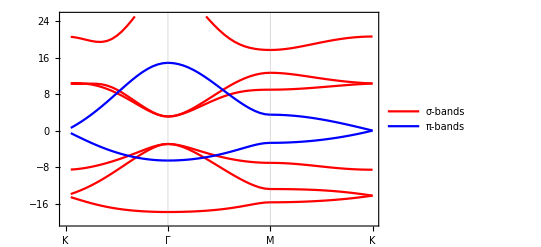

```mathematica
bandsπ=Table[Sort@Chop@Eigenvalues[{Hpzpz,Spzpz}/.k->klist⟦i⟧],{i,Length[klist]}];
bandsσ=Table[Sort@Chop@Eigenvalues[{H⟦1;;6,1;;6⟧,S⟦1;;6,1;;6⟧}/.k->klist⟦i⟧],{i,Length[klist]}];

ListLinePlot[Join[Transpose[bandsσ],Transpose[bandsπ]],
PlotStyle->{Red,Red,Red,Red,Red,Red,Blue,Blue},Axes->False,Frame->True,
PlotRange->{-20,25},PlotLegends->Placed[LineLegend[Automatic,{"σ-bands","π-bands"}],Right],
FrameTicks->{{{0,"K"},{20,"Γ"},{40,"M"},{60,"K"}},Automatic},GridLines->{{20,40},None}]
```

The obtained band structure is the same as that one in Fig. 6 of R. Saito, M. Fujita, G. Dresselhaus, and M. S. Dresselhaus, Phys. Rev. B 46, 1804 (1992) or Fig. 2.8 on page 32 in  R. Saito, G. Dresselhaus, and M. Dresselhaus, Physical Properties of Carbon Nanotubes (Imperial College Press, London, 1998).

### Summary

To summarize, Hamiltonian can be used to construct building blocks of the multi-orbital tight-binding Hamiltonian. The size of each block is defined by the number of atomic sites in the structure, the number of such block required for the full multi-orbital Hamiltonian is defined by the number of basis orbitals used to represent the structure. In the above cases the type and number of basis orbitals was the same for all the atoms in the crystal lattice. It can happen, however, that composition of the crystal require usage of the different number and type of atomic orbital for different sites. In this complicated case, the above mentioned structure of the multi-orbital Hamiltonian also applies. The major difference will be that the final matrix will contain 'empty' rows and columns fully composed of zeros. Hence, before solving the eigenvalue problem this matrix must be refined by deleting the empty rows and columns.

More About

Related Tutorials

Related Wolfram Education Group Courses